## Definitions

### One photon entanglement (Theorem 1)

```mathematica
(*Misc*)
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]];
$HistoryLength=10;


F1[ξ_,coeffs_]:=With[
{m=Length@coeffs},
-Sum[Sqrt[1-coeffs[[i]] ξ],{i,1,m-1}]-Sqrt[1-coeffs[[m]] ξ]+m-2
]
F2[ξ_,coeffs_]:=With[
{m=Length@coeffs},
-Sum[Sqrt[1-coeffs[[i]] ξ],{i,1,m-1}]+Sqrt[1-coeffs[[m]] ξ]+m-2
]
f0[coeffs_]:=With[
{m=Length@coeffs},
-Sum[Sqrt[1-coeffs[[i]]/coeffs[[m]]],{i,1,m-1}]+m-2
]

g1[ξ_,coeffs_]:=With[
{m=Length@coeffs},
1/(2^(m-2)ξ)Product[(1+Sqrt[1-coeffs[[i]]ξ]),{i,1,m-1}](1+Sqrt[1-coeffs[[m]]ξ])
]
g2[ξ_,coeffs_]:=With[
{m=Length@coeffs},
1/(2^(m-2)ξ)Product[(1+Sqrt[1-coeffs[[i]]ξ]),{i,1,m-1}](1-Sqrt[1-coeffs[[m]]ξ])
]

findZeroInInterval[foo_,xMin_,xMax_]:=Module[
{ϵ=10^-10},
If[foo@xMax==0,Return[xMax]];
If[foo@xMin==0,Return[xMin]];

(*findRoot does not like edge values (as in foo[x] is fine, but foo[x+ϵ] is complex). So choose foo[x-ϵ]. But first make sure, that foo[x-ϵ] has the same sign as foo[x], so that ϵ is chosen sufficiently small. Lower by an order of magnitude each step*)
While[Sign@foo@xMax!=Sign@foo[xMax-ϵ],ϵ/=10];

x/.FindRoot[foo[x],{x,xMin,xMax-ϵ},Method->"Brent"]
]

(*Subscript[F, 2] has the root at ξ=0 in addition to the second root. Instead of going the route from the paper, using the derivative of Subscript[F, 2], we use the sign of Subscript[F, 2]. Since Subscript[F, 2]'(0) > 0 (stated here without proof), we know that, if Subscript[F, 2] has two roots, Subscript[F, 2](Subscript[ξ, max])<0. Hence we half the search interval until Subscript[F, 2] > 0, giving us a search interval for Subscript[F, 2] that has a single root *)
findξMinForF2[coeffs_]:=Module[
{ξMax=1/coeffs[[-1]],ξMin},
ξMin=ξMax/2;
While[F2[ξMin,coeffs]<0,
ξMin/=2;
];

ξMin
]

putMaxElementLast[l_]:=With[
{argMax=First@PositionLargest[l]},
Join[Delete[l,argMax],{l[[argMax]]}]
]

sepValOnePhoton[λ_]:=Module[
{coeffs,ξMax,whichF,ξMin,F,ξ0},
(*Ensure that max element is last, and work with the squared absolute values*)
coeffs=putMaxElementLast[Abs[λ]^2];

(*Subscript[λ, M]^2>= 1/2 ? If so, we're done*)
If[coeffs[[-1]]>=0.5,Return[coeffs[[-1]]]];

ξMax=1/coeffs[[-1]];

whichF=If[f0[coeffs]>=0,1,2];
ξMin=If[whichF==1,0,findξMinForF2[coeffs]];

F=If[whichF==1,
F1[#,coeffs]&,
F2[#,coeffs]&
];

ξ0=findZeroInInterval[F,ξMin,ξMax];

If[whichF==1,
g1[ξ0,coeffs],
g2[ξ0,coeffs]
]
]

wStateDifferentPartition[state_,partition_]:=Sum[Sqrt[Sum[Abs[state[[i]]]^2,{i,partition[[k]]}]]UnitVector[Length@partition,k],{k,1,Length@partition}]

(*n coordinates corresponding to a random point on the (n-1)-sphere*)
randomPointsOnSphere[n_]:=Normalize@RandomVariate[NormalDistribution[],n]
```

### Entanglement of bipartitions (Sec. IV.A)

```mathematica
(*get the number of possible fock states for m modes and n photons*)
numFockStates[m_,n_]:=(m-1+n)!/( (m-1)!n! )

(*given that the number of non-zero entries for the case of constant photon numbers grows slower than for a general (N+1)^M number of entries, we will use sparse arrays*)
(*N+1, since for N photons we can have the N+1 states |0>,|1>,...,|N>*)
createStateVector[m_,n_]:=SparseArray[{},ConstantArray[n+1,m],0.0]

getM[ψ_]:=Length@Dimensions@ψ
getN[ψ_]:=Dimensions[ψ][[1]]-1

(*<1,0,2|ψ> would correspond to ψ[[2,1,3]]=getStateElement[ψ,{1,0,2}]*)
getStateElement[ψ_,multiIndex_]:=With[
{m=getM@ψ,n=getN@ψ},
If[Length@multiIndex!=m,Print["getStateElement: wrong number of modes!"]];
ψ[[##]]&@@(multiIndex+1)
]

(*instead of writing ψ[[2,1,3]]=α, write ψ=setStateElement[ψ,{1,0,2},α]*)
setStateElement[ψ_,multiIndex_,newVal_]:=With[
{m=getM@ψ,n=getN@ψ},
If[Length@multiIndex!=m,Print["setStateElement: wrong number of modes!"]];
If[Total@multiIndex!=n,Print["setStateElement: wrong number of photons!"]];
ReplacePart[ψ,multiIndex+1->newVal]
]

(*get all elements in ψ that have a constant photon number of N in a table*)
fullStateVector[ψ_]:=With[
{m=getM@ψ,n=getN@ψ},
Table[
{fock,getStateElement[ψ,fock]},
{fock,fockSum[m,n]}]
]

normalizeStateVector[ψ_]:=ψ/Sqrt@Total[ψ**ψ,Infinity]

(*expand a vector. Gives vector where `list[[i]]` occurs `times[[i]]` times*)
expandVector[list_,times_]:=Flatten@Table[ConstantArray[list[[i]],times[[i]]],{i,1,Length@list}]

(*expand a matrix. Gives a matrix where the row `mat[[i,.]]` occurs `rows[[i]]` times and the column `mat[[.,j]]` occurs `columns[[j]]` times. Also works on non-square matrices.*)
(*In the notation by Scheel this means:
For a p x q matrix Λ and the arguments
- rows = {t_1,t_2,...,t_p}
 - columns = {n_1,n_2,...,n_q}
this gives the matrix Λ[(1^t_1, 2^t_2, ..., p^t_p)|(1^n_1, 2^n_2, ..., q^n_q)] 
*)
expandMatrix[mat_,rows_,columns_]:=Table[
mat[[i,j]],
{i,expandVector[Range[Dimensions[mat][[1]]],rows]},
{j,expandVector[Range[Dimensions[mat][[2]]],columns]}
]

(*Gives <fockOut|out> where |out> is the output of entering a single fock state `fockIn` into the LON described by U, i.e. a -> Ua.
In the notation used so far, we input |n_1,...,n_M⟩ and look at ⟨t_1,...,t_M|out⟩*)
photNetworkFockElement[fockOut_,fockIn_,U_]:=1/Sqrt[Product[fockIn[[i]]!,{i,1,Length@fockIn}]]*1/Sqrt[Product[fockOut[[i]]!,{i,1,Length@fockOut}]]*Permanent[expandMatrix[U,fockOut,fockIn]]

(*give iterable for sums of the form sum_{Subscript[n, i] ∈ Subscript[N, 0]: Subscript[n, 1]+...+Subscript[n, M] = N}
every unique combination is given exactly once with ordering taken into account.
E.g. fockSum[3,2]={{2,0,0},{0,2,0},{0,0,2},{1,1,0},{1,0,1},{0,1,1}}*)
fockSum[m_,n_]:=Flatten[Permutations/@IntegerPartitions[n,{m},Range[0,n]],1]

(*apply the network U to the state vector ψ*)
applyNetwork[ψ_,U_]:=Module[
{elems=Table[{First@rule-1,First@rule/.rule},{rule,ArrayRules[ψ][[;;-2]]}],m=getM@ψ,n=getN@ψ,ψNew},
If[m!=Length@U,"applyNetwork: Wrong dimension of U!"];
ψNew=createStateVector[m,n];
Do[
ψNew+=ψIn[[2]]*ReplacePart[createStateVector[m,n],Table[fockOut+1->photNetworkFockElement[fockOut,ψIn[[1]],U],{fockOut,fockSum[m,n]}]],
{ψIn,elems}
];
SparseArray@ψNew
]

(*turns a (Fock state) multi index to the index of a corresponding list. E.g. for N=2 Photons and M=3 modes:
|000>->1, |001>->2, |002>->3, |010>->4, ..., |222>->27 
For N=2 Photons we would need to call this function with multiIndToInd[{..},N+1] since for N=2 photons I have N+1=3 options per mode: 0,1,2*)
multiIndToInd[multiInd_,n_]:=Sum[n^(Length@multiInd-i-1)multiInd[[i+1]],{i,0,Length@multiInd-1}]+1

schmidtCoeffsSubSpace[ψ_,t_,k_,permutation_]:=Module[
{m=getM@ψ,n=getN@ψ,coeffM,i,j,σ},
If[k<1||k>=m,Print["k needs to fulfill: 1<=k<M!"]];
(*σ[{i,j,k,l}] for permutation=={4,1,3,2} gives {l,i,k,j}*)
σ[inds_]:=Part[inds,InversePermutation@permutation];
coeffM=SparseArray[{},{(t+1)^k,(n-t+1)^(m-k)},0.0];
Do[
i=multiIndToInd[multI,t+1];
j=multiIndToInd[multJ,n-t+1];
coeffM[[i,j]]=getStateElement[ψ,σ@Join[multI,multJ]],
{multI,fockSum[k,t]},{multJ,fockSum[m-k,n-t]}
];
SingularValueList[coeffM,1]
]

sepValBipartition[ψ_,k_,permutation_:{}]:=Module[
{σ},
If[Length@permutation==0,σ=Range[getM@ψ],σ=permutation];
Max@Table[Abs[schmidtCoeffsSubSpace[ψ,t,k,σ]]^2,{t,0,getN@ψ}]
]

(*get all bipartitions in the following format:
{{k,{Subscript[σ, 1],Subscript[σ, 2],...}}, ...} where k=2 and σ={4,5,1,2,3} would correspond to the partition {4,5}:{1,2,3}
Duplicates are not present*)
allBipartitions[m_]:=With[
{inds=Range@m},
Table[{
k,
Join[#,Complement[inds,#]]&/@If[k==m/2,(*{1,2}:{3,4} is the same as {3,4}:{1,2}*)
Cases[Subsets[inds,{k}],_?(MemberQ[#,1]&)],(*so only keep the ones where 1 is in the first partition*)
Subsets[inds,{k}]
]
},
{k,1,Floor[m/2]}]
]

(*get the sep vals for all possible bipartitions returns list with the following elements:
{P1,P2,g}, where e.g. P1={1,2},P2={3,4} for bipartition P1:P2*)
sepValsAllBipartitions[ψ_]:=With[
{biparts=allBipartitions@Length@Dimensions@ψ},
ArrayFlatten[Table[
{σ[[1;;part[[1]]]],σ[[part[[1]]+1;;]],sepValBipartition[ψ,part[[1]],σ]},
{part,biparts},{σ,part[[2]]}](*part[[1]]==k*),
1]
]

(*return the max element from the output of SepValsAllBipartitions*)
genuineMultiPartiteEntanglement[sepValList_]:=Max[sepValList[[All,3]]]

(*return random unitary mxm matrix. c.f. code from http://home.lu.lv/~sd20008/papers/essays/Random%20unitary%20[paper].pdf, Sec. 3.1*)
randomUnitary[m_]:=Orthogonalize@Table[RandomReal[NormalDistribution[]]+I*RandomReal[NormalDistribution[]],{m},{m}]
```

### Hadamard walk

```mathematica
(*posNum=3;
modeNum=2posNum;
Σ=IdentityMatrix[posNum];
Σ=AppendTo[Σ[[2;;]],Σ[[1]]];
U=1/Sqrt[2]ArrayFlatten[{{Σ,Σ},{Σᵀ,-Σᵀ}}];
initState[c_,x_]:=UnitVector[modeNum,posNum*c+x+1]
evolveState[state_,t_]:=MatrixPower[U,t,state]
takeStep[state_]:=U.state
cpToM[c_,x_]:=posNum*c+x+1 (*coin and position index to mode index*)*)

UHadWalk[p_]:=Module[
{Σ=IdentityMatrix[p]},
Σ=Join[Σ[[2;;]],{Σ[[1]]}];
1/Sqrt@2ArrayFlatten[{{Σ,Σ},{Σᵀ,-Σᵀ}}]
]

initState[p_,c_,x_]:=UnitVector[2p,p*c+x+1]
cpToM[p_,c_,x_]:=p*c+x+1 (*coin and position index to mode index*)
evolveState[U_,state_,t_]:=MatrixPower[U,t,state]
takeStep[U_,state_]:=U.state
```

```mathematica
(*Integral I(n)*)
int[-1]=1;
int[n_]:=int[n]=Sum[(-1)^k Binomial[2k,k]1/4^k,{k,0,Floor[(n-1)/2]}]

(*relates to coin entanglement for QW on a line*)
ϕ1[n_,θ_,ϕ_]:=Sin[θ/2]^2+Cos[θ] int[n]/2+Sin[θ]Cos[ϕ](int[n-1]-1)/2
(*Entanglement on the line Subscript[E, g]=1-Subscript[g, max]*)
coinEntLine[n_,θ_,ϕ_]:=Min[#,1-#]&@ϕ1[n,θ,ϕ]
```

## Applications (Secs. III and IV)

### Random one-photon networks (Sec. III.A)

```mathematica
sepValEW[m_]:=((m-1)/m)^(m-1)(*sep val equally weighted W state*)
equidistantLogPoints[min_,max_,n_]:=Table[10^i,{i,Range[Log10@min,Log10@max,(Log10@max-Log10@min)/n]}]

howMany=5000;
quantile=0.68;
modeNumbersFine=Floor@N@equidistantLogPoints[2,200,50]
modeNumbersCoarse=Floor@N@equidistantLogPoints[200,10^5,200]
modeNumbers=DeleteDuplicates@Join[modeNumbersFine,modeNumbersCoarse]
Length@modeNumbers

randomW=Table[
data=ParallelTable[1-sepValOnePhoton[randomPointsOnSphere[m]],howMany];
Join[{m, Mean[data]},Quantile[data,{1-quantile,quantile}]],
{m,modeNumbers}
];//AbsoluteTiming

Export["Random-one-photon.csv",randomW]
```

{2,2,2,2,2,3,3,3,4,4,5,5,6,6,7,7,8,9,10,11,12,13,15,16,18,19,21,24,26,28,31,34,38,41,45,50,55,60,66,72,79,87,95,104,115,126,138,151,166,182,200}

{200,206,212,219,226,233,240,248,256,264,272,281,290,299,308,318,328,339,349,360,372,384,396,408,421,434,448,462,477,492,508,524,540,557,575,593,612,631,651,671,693,715,737,760,784,809,835,861,888,916,945,975,1006,1038,1070,1104,1139,1175,1212,1250,1290,1331,1373,1416,1461,1507,1554,1603,1654,1706,1760,1816,1873,1932,1993,2056,2121,2188,2257,2328,2402,2478,2556,2636,2720,2806,2894,2985,3080,3177,3277,3381,3487,3597,3711,3828,3949,4074,4202,4335,4472,4613,4758,4909,5064,5223,5388,5558,5734,5915,6101,6294,6493,6698,6909,7127,7352,7584,7823,8070,8325,8588,8859,9138,9427,9724,10031,10348,10675,11011,11359,11718,12087,12469,12862,13268,13687,14119,14565,15024,15499,15988,16492,17013,17550,18104,18675,19265,19873,20500,21147,21814,22503,23213,23946,24701,25481,26285,27115,27971,28853,29764,30704,31673,32672,33703,34767,35864,36996,38164,39369,40611,41893,43215,44579,45986,47437,48934,50479,52072,53715,55411,57160,58964,60825,62744,64725,66767,68875,71048,73291,75604,77990,80451,82990,85610,88312,91099,93974,96940,100000}

{2,3,4,5,6,7,8,9,10,11,12,13,15,16,18,19,21,24,26,28,31,34,38,41,45,50,55,60,66,72,79,87,95,104,115,126,138,151,166,182,200,206,212,219,226,233,240,248,256,264,272,281,290,299,308,318,328,339,349,360,372,384,396,408,421,434,448,462,477,492,508,524,540,557,575,593,612,631,651,671,693,715,737,760,784,809,835,861,888,916,945,975,1006,1038,1070,1104,1139,1175,1212,1250,1290,1331,1373,1416,1461,1507,1554,1603,1654,1706,1760,1816,1873,1932,1993,2056,2121,2188,2257,2328,2402,2478,2556,2636,2720,2806,2894,2985,3080,3177,3277,3381,3487,3597,3711,3828,3949,4074,4202,4335,4472,4613,4758,4909,5064,5223,5388,5558,5734,5915,6101,6294,6493,6698,6909,7127,7352,7584,7823,8070,8325,8588,8859,9138,9427,9724,10031,10348,10675,11011,11359,11718,12087,12469,12862,13268,13687,14119,14565,15024,15499,15988,16492,17013,17550,18104,18675,19265,19873,20500,21147,21814,22503,23213,23946,24701,25481,26285,27115,27971,28853,29764,30704,31673,32672,33703,34767,35864,36996,38164,39369,40611,41893,43215,44579,45986,47437,48934,50479,52072,53715,55411,57160,58964,60825,62744,64725,66767,68875,71048,73291,75604,77990,80451,82990,85610,88312,91099,93974,96940,100000}

241

{32625.,Null}

Random-one-photon.csv

### Quantum walk (Secs. III.B and III.C)

#### Entanglement Dynamics P=4 and P=8

{0.0016162,Null}

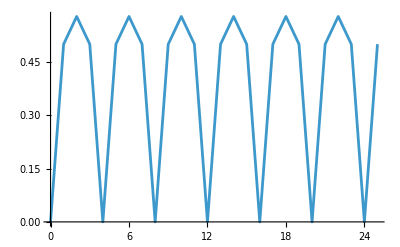

HW-full-N=1-P=4-n=25.csv

```mathematica
p=4;
U=UHadWalk[p];
maxT=25;
state=N[initState[p,0,0]];
entDyn=Join[
{{0,1-sepValOnePhoton[state]}},
Table[ 
state=takeStep[U,state];
{n,1-sepValOnePhoton[state]},
{n,1,maxT}
]
];//AbsoluteTiming

ListPlot[entDyn,Joined->True]

Export["HW-full-N=1-P="<>ToString@p<>"-n="<>ToString@maxT<>".csv",entDyn]
```

{0.0024809,Null}

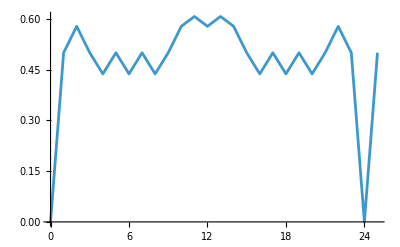

HW-full-N=1-P=8-n=25.csv

```mathematica
p=8;
U=UHadWalk[p];
maxT=25;
state=N[initState[p,0,0]];
entDyn=Join[
{{0,1-sepValOnePhoton[state]}},
Table[ 
state=takeStep[U,state];
{n,1-sepValOnePhoton[state]},
{n,1,maxT}
]
];//AbsoluteTiming

ListPlot[entDyn,Joined->True]

Export["HW-full-N=1-P="<>ToString@p<>"-n="<>ToString@maxT<>".csv",entDyn]
```

#### Entanglement Dynamics P=3 and P=6

{0.0056445,Null}

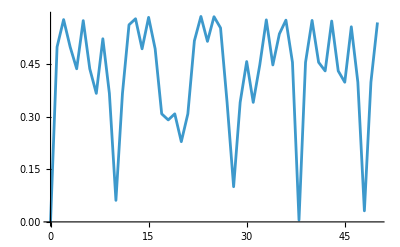

HW-full-N=1-P=3-n=50.csv

```mathematica
p=3;
U=UHadWalk[p];
maxT=50;
state=N[initState[p,0,0]];
entDyn=Join[
{{0,1-sepValOnePhoton[state]}},
Table[ 
state=takeStep[U,state];
{n,1-sepValOnePhoton[state]},
{n,1,maxT}
]
];//AbsoluteTiming

ListPlot[entDyn,Joined->True]

Export["HW-full-N=1-P="<>ToString@p<>"-n="<>ToString@maxT<>".csv",entDyn]
```

```mathematica
p=6;
U=UHadWalk[p];
maxT=50;
state=N[initState[p,0,0]];
entDyn=Join[
{{0,1-sepValOnePhoton[state]}},
Table[ 
state=takeStep[U,state];
{n,1-sepValOnePhoton[state]},
{n,1,maxT}
]
];//AbsoluteTiming

ListPlot[entDyn,Joined->True]

Export["HW-full-N=1-P="<>ToString@p<>"-n="<>ToString@maxT<>".csv",entDyn]
```

{0.0051943,Null}

-Graphics-

HW-full-N=1-P=6-n=50.csv

#### Entanglement Dynamics P=500

{121.136,Null}

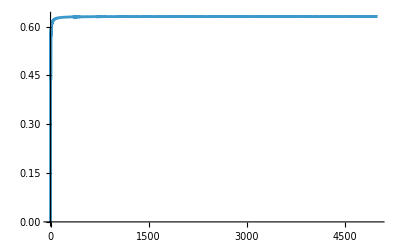

HW-full-N=1-P=500-n=5000.csv

```mathematica
p=500;
U=UHadWalk[p];
maxT=5000;
state=N[initState[p,0,0]];
entDyn=Join[
{{0,1-sepValOnePhoton[state]}},
Table[ 
state=takeStep[U,state];
{n,1-sepValOnePhoton[state]},
{n,1,maxT}
]
];//AbsoluteTiming

ListPlot[entDyn,Joined->True]

Export["HW-full-N=1-P="<>ToString@p<>"-n="<>ToString@maxT<>".csv",entDyn]
```

```mathematica
(*Showcasing the oscillatory behavior*)
entDynR=entDyn[[;;250]][[All,2]]
maxs=FindPeaks[entDynR,0,InterpolationOrder->0][[All,1]]
mins=FindPeaks[-entDynR,0,InterpolationOrder->0][[All,1]]

Print["Differences:"]
maxs[[2;;]]-maxs[[;;-2]]
mins[[2;;]]-mins[[;;-2]]
```

{0.,0.5,0.578125,0.5,0.4375,0.5,0.569556,0.593789,0.590014,0.573864,0.571846,0.584047,0.597771,0.604115,0.602695,0.597689,0.597002,0.601102,0.607157,0.610203,0.609651,0.607358,0.60699,0.608917,0.612112,0.613892,0.613896,0.61265,0.612329,0.61338,0.615365,0.616541,0.616629,0.615882,0.615742,0.616384,0.617644,0.618447,0.618593,0.618137,0.618062,0.618491,0.619394,0.619946,0.620046,0.619758,0.619768,0.6201,0.620747,0.621121,0.621209,0.621012,0.621049,0.621335,0.621846,0.622104,0.622145,0.621991,0.62207,0.62233,0.622734,0.622919,0.622935,0.622803,0.622887,0.623126,0.623482,0.62362,0.623599,0.623478,0.623569,0.623793,0.624105,0.624213,0.624181,0.624064,0.624139,0.624349,0.624639,0.62473,0.624686,0.624568,0.624635,0.62483,0.625092,0.625175,0.625133,0.625015,0.625067,0.625243,0.625488,0.625569,0.625524,0.62541,0.625453,0.62561,0.625833,0.625911,0.625873,0.625766,0.625795,0.625934,0.626142,0.626216,0.626182,0.626083,0.626106,0.626228,0.626416,0.626486,0.626461,0.626369,0.626385,0.626494,0.626665,0.626731,0.626709,0.626626,0.626641,0.626737,0.626891,0.626952,0.626935,0.62686,0.626873,0.626959,0.6271,0.627155,0.627138,0.627071,0.627085,0.627164,0.627291,0.62734,0.627326,0.627265,0.627278,0.627352,0.627469,0.627512,0.627498,0.627441,0.627457,0.627526,0.627633,0.627672,0.627658,0.627605,0.62762,0.627685,0.627787,0.627821,0.627805,0.627756,0.627771,0.627834,0.627929,0.62796,0.627944,0.627896,0.627911,0.627971,0.628062,0.62809,0.628074,0.628027,0.628041,0.628099,0.628185,0.628212,0.628196,0.62815,0.628163,0.628218,0.628301,0.628327,0.62831,0.628266,0.628277,0.628329,0.628408,0.628433,0.628418,0.628375,0.628384,0.628434,0.62851,0.628534,0.628519,0.628477,0.628486,0.628532,0.628604,0.628628,0.628615,0.628575,0.628582,0.628625,0.628694,0.628717,0.628704,0.628666,0.628673,0.628714,0.628779,0.628801,0.628789,0.628754,0.628759,0.628797,0.628859,0.62888,0.628869,0.628836,0.628841,0.628877,0.628936,0.628956,0.628946,0.628914,0.628919,0.628953,0.629009,0.629027,0.629017,0.628987,0.628993,0.629026,0.629078,0.629096,0.629086,0.629057,0.629063,0.629094,0.629145,0.629161,0.629151,0.629123,0.629129,0.62916,0.629209,0.629223,0.629214,0.629187,0.629193,0.629223,0.629269,0.629284,0.629274,0.629247}

{3,8,14,20,27,33,39,45,51,57,63,68,74,80,86,92,98,104,110,116,122,128,134,140,146,152,158,164,170,176,182,188,194,200,206,212,218,224,230,236,242,248}

{1,5,11,17,23,29,35,41,46,52,58,64,70,76,82,88,94,100,106,112,118,124,130,136,142,148,154,160,166,172,178,184,190,196,202,208,214,220,226,232,238,244,250}

Differences:

{5,6,6,7,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

{4,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

#### Density plots for varying the initial conditions

```mathematica
p=5;
U=UHadWalk[p];
dθ=0.01Pi;
dϕ=0.01Pi;
θVals=Range[0,Pi,dθ];
ϕVals=Range[0,2Pi,dϕ];

valsN2=Table[
state=N[Cos[θ/2]initState[p,0,0]+Exp[I ϕ]Sin[θ/2] initState[p,1,0]];
1-sepValOnePhoton[evolveState[U,state,2]],
{θ,θVals},{ϕ,ϕVals}
];//AbsoluteTiming
valsN5=Table[
state=N[Cos[θ/2]initState[p,0,0]+Exp[I ϕ]Sin[θ/2] initState[p,1,0]];
1-sepValOnePhoton[evolveState[U,state,4]],
{θ,θVals},{ϕ,ϕVals}
];//AbsoluteTiming
valsCoinEnt=Table[
ϕ1Asymp=1/2-(Sqrt[2]-1)/(2Sqrt[2])(Cos[θ]+Sin[θ]Cos[ϕ]);
Min[ϕ1Asymp,1-ϕ1Asymp],
{θ,θVals},{ϕ,ϕVals}
];//AbsoluteTiming

ListDensityPlot[valsN2]
ListDensityPlot[valsN5]
ListDensityPlot[valsCoinEnt]

Export["HW-ICs-Thetas.csv",θVals]
Export["HW-ICs-Phis.csv",ϕVals]
Export["HW-ICs-N=1-P=5-n=2.csv",valsN2]
Export["HW-ICs-N=1-P=5-n=4.csv",valsN5]
Export["HW-ICs-Coin_Ent-Asymptotic.csv",valsCoinEnt]
```

{3.82286,Null}

{2.46364,Null}

{0.189866,Null}

-Graphics-

-Graphics-

-Graphics-

HW-ICs-Thetas.csv

HW-ICs-Phis.csv

HW-ICs-N=1-P=5-n=2.csv

HW-ICs-N=1-P=5-n=4.csv

HW-ICs-Coin_Ent-Asymptotic.csv

#### Varying the initial conditions from asymmetric to symmetric

{1.48263,Null}

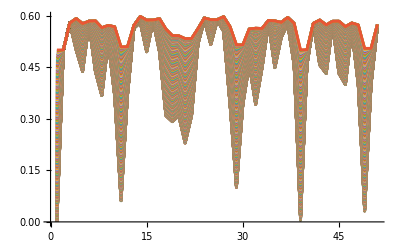

HW-ICs-Sym-To-Asym-P=3-n=50.csv

```mathematica
p=3;
U=UHadWalk[p];

θVals=Range[0,Pi/2,0.002Pi];
nVals=Range[1,50];

vals=Table[
state=N[Cos[θ/2]initState[p,0,0]+Exp[I Pi/2]Sin[θ/2] initState[p,1,0]];
1-Join[
{sepValOnePhoton[state]},
Table[
state=takeStep[U,state];
sepValOnePhoton[state],
{n,nVals}]
],
{θ,θVals}
];//AbsoluteTiming
PrependTo[nVals,0];

allVals=ArrayFlatten[
{
{{{-1}},{θVals}},
{{nVals}ᵀ,valsᵀ}
}
];

ListPlot[vals,Joined->True]

Export["HW-ICs-Sym-To-Asym-P=3-n=50.csv",allVals]
```

#### Entanglement dynamics for different partitions

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{{0,0.,0.,0.,0}}

{0.194824,Null}

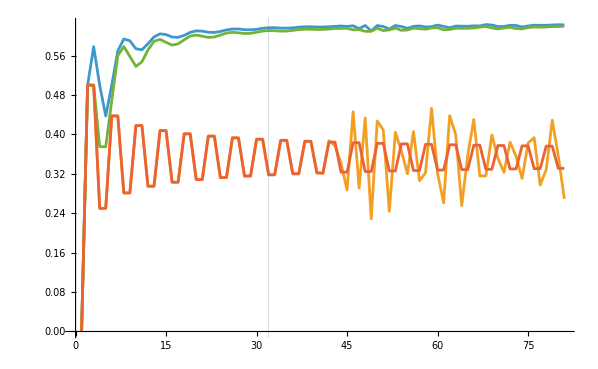

HW-diff_parts-N=1-P=64-n=100.csv

```mathematica
p=64;
U=UHadWalk[p];

state=initState[p,0,0]//N
partitionCoin={Range[1,p],Range[p+1,p]};
partitionPos=Table[{i,p+i},{i,1,p}];

startEnt={{
0, 
1-sepValOnePhoton[state],
1-sepValOnePhoton[wStateDifferentPartition[state,partitionCoin]],
1-sepValOnePhoton[wStateDifferentPartition[state,partitionPos]],
0
}}
vals=Table[
state=takeStep[U,state];
{
n,
1-sepValOnePhoton[state],
1-sepValOnePhoton[wStateDifferentPartition[state,partitionCoin]],
1-sepValOnePhoton[wStateDifferentPartition[state,partitionPos]],
ϕ1[n,0,0]
},
{n,1,80}
];//AbsoluteTiming

vals=Join[startEnt,vals];

ListPlot[
valsᵀ[[2;;]],
Joined->True,
GridLines->{{32},{}}
]

Export["HW-diff_parts-N=1-P=64-n=100.csv",N[vals]]
```

### Multiple walkers and genuine multipartite entanglement (Sec. IV.C)

```mathematica
maxSepValRandomNetwork[ψin_]:=genuineMultiPartiteEntanglement[sepValsAllBipartitions[applyNetwork[ψin,randomUnitary@getM@ψin]]]

howMany=6000;
quantile=0.68;
```

#### constant M, vary N

```mathematica
vals=Table[
Flatten@Join[{n}, Table[
ψin=createStateVector[m,n];
ψin=setStateElement[ψin,Join[{n},ConstantArray[0,m-1]],1];(*N0...0*)
data=ParallelTable[1-Quiet[maxSepValRandomNetwork[ψin]],howMany];
Flatten[{Mean[data],Quantile[data,{1-quantile,quantile}]}],
{m,2,6}
]],
{n,1,10}
];//AbsoluteTiming

Export["GME_over_N-Random-M=2_to_6-N=1_to_10.csv",vals]
```

{7200.86,Null}

GME_over_N-Random-M=2_to_6-N=1_to_10.csv

#### constant N, vary M

```mathematica
vals=Table[
Flatten@Join[{m}, Table[
ψin=createStateVector[m,n];
ψin=setStateElement[ψin,Join[{n},ConstantArray[0,m-1]],1];(*N0...0*)
data=ParallelTable[1-Quiet[maxSepValRandomNetwork[ψin]],howMany];
Flatten[{Mean[data],Quantile[data,{1-quantile,quantile}]}],
{n,1,4}
]],
{m,2,10}
];//AbsoluteTiming

Export["GME_over_M-Random-M=2_to_10-N=1_to_4.csv",vals]
```

{16295.4,Null}

GME_over_M-Random-M=2_to_10-N=1_to_4.csv